# ANOMS ANZ@SFO Data Analysis

This is the real deal, 4/1/2015 notwithstanding

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/Desktop Stuff/ANOMS/SFO ANOMS"]
```

/Users/brucesawhill/Desktop/Desktop Stuff/ANOMS/SFO ANOMS

```mathematica
sfoanomsdays=FileNames[];
Length[sfoanomsdays]
sfoanomsdays[[1]]//FullForm  (* a sample *)
```

280

"20060201.lt6"

```mathematica
SetDirectory["/Users/brucesawhill/Desktop/Desktop Stuff/ANOMS/SFO ANOMS"]
```

/Users/brucesawhill/Desktop/Desktop Stuff/ANOMS/SFO ANOMS

Accessory Functions

This plots the location of the aircraft when making a video

```mathematica
acpointplot[proxdata_,pingindex_] := 
 Show[DeleteCases[Table[If[Length[proxdata[[i,pingindex]]]==2, ListPlot[{proxdata[[i,pingindex]]}, 
   PlotRange -> {{-120000, 120000}, {-120000, 120000}}, 
   PlotStyle -> {PointSize[1/24], Opacity[0.2], If[i==1,Red,Blue]}]],{i,Length[proxdata]}],Null]]
```

```mathematica
castable[nzindex_]:=Table[
{filterednzflights[[nzindex, j +2, 3]], 
1.944 * Sqrt[densitylowratio[filterednzflights[[nzindex, j+2, 3]]]] *Sqrt[(filterednzflights[[nzindex, j+4, 1]] - filterednzflights[[nzindex, j, 1]])^2 + (filterednzflights[[nzindex,j+4,2]]-filterednzflights[[nzindex, j, 2]])^2]/(filterednzflights[[nzindex, j+4, 5]]-filterednzflights[[nzindex, j, 5]]),filterednzflights[[nzindex, j, 5]]},{j,21, Length[filterednzflights[[nzindex]]]-4}
]
```

```mathematica
castable2[nzindex_]:=
Table[
{
filterednzflights[[nzindex, j , 3]],filterednzflights[[nzindex,j,4]]*1.944 * Sqrt[densitylowratio[filterednzflights[[nzindex, j, 3]]]]
},{j,21, Length[filterednzflights[[nzindex]]]}
]
```

This plots the contrail leading up to the aircraft when making a video

```mathematica
contrailplot[proxdata_,pingindex_]:=
{
contrails =Table[{},{Length[proxdata]}];
 
Do[contrails[[i]] = 
Table[
If[
Length[proxdata[[i,j]]]≠2, Null,proxdata[[i,j]]
],{j,1,pingindex}
],{i,Length[proxdata]}
];

For[i = 1,i <= Length[contrails], i++, 
{
If[contrails[[i,-1]]==Null , contrails[[i]]=={{}}];
DeleteCases[contrails[[i]],Null]
}
];

DeleteCases[contrails, {{}}];

Show[
Table[
ListPlot[
contrails[[i]],PlotRange->{{-100000,100000},{-100000,100000}},Joined->True
], {i, Length[contrails]}
]
]
}[[1]]
```

```mathematica
convertdegminsectodecimal[degminsec_]:=
{a=StringPosition[degminsec, "-"];
deg =ToExpression[ StringTake[degminsec, {1, a[[1,1]]-1}]];
min = ToExpression[StringTake[degminsec, {a[[1,1]]+1,a[[2,1]]-1}]];
sec = ToExpression[StringTake[degminsec, {a[[2,1]]+1, -1}]];
decimalform = deg + min/60.+sec/3600.
}[[1]]
```

```mathematica
densitylowratio[h_]:=(1-2.255 10^-5 h)^4.2541
```

```mathematica
distance[flight_]:=Sum[flight[[i,4]] (flight[[i+1,5]]-flight[[i,5]]),{i,21, Length[flight]-1}]
```

```mathematica
distanceabovealtitude[flight_,cutoff_]:=Sum[If[flight[[i,3]]>cutoff,flight[[i,4]] (flight[[i+1,5]]-flight[[i,5]]),0],{i,21, Length[flight]-1}]
```

```mathematica
distancefilter[lowerbound_,upperbound_]:=
DeleteCases[Table[If[nzdistances[[i]]≥lowerbound && nzdistances[[i]]<upperbound, i,0],{i,Length[nzdistances]}],0]
```

```mathematica
filenumbers[indexlist_,groupname_]:=
{
filenos = Table[0, {Length[indexlist]}];
Do[
{dateinfo=Take[filterednzflights[[groupname[[indexlist[[i]]]]]],{3}][[1,1]],
datadate=StringJoin["20",StringTake[dateinfo,{9,10}],StringTake[dateinfo,2],StringTake[dateinfo,{4,5}],".lt6"],
filenos[[i]]={Position[sfoanomsdays,datadate][[1,1]],dateinfo}
},{i,Length[indexlist]}];
filenos
}[[1]]
```

```mathematica
interpolated[data_]:=
(*  Takes unevenly sampled data and generates a data point every second for the
duration of the data *)
{
offsettime = AbsoluteTime[StringJoin[data[[3,1]],"/",data[[4,1]]]];
ld = Length[data];
totaltime = data[[ld,5]];
newdatatable =Table[{},{totaltime+1}]; (* Make a one-second resolution dataset*)
newdatatable[[1]] = data[[21]];
p = 2;(* Set interpolating index *)

Do[
diff = data[[i+1,5]]-data[[i,5]];
Do[
{
newdatatable[[p]]=(diff-j)/diff data[[i]]+j/diff data[[i+1]]; (* Interpolate *)
p++
}
,{j, 1, diff}
]
,{ i, 21,ld-1}
]
Do[newdatatable[[k,5]]=newdatatable[[k,5]]+offsettime, {k, totaltime+1}];
newdatatable
}
```

```mathematica
latdistconvert[latref_,lat2_]:=
(lat2-latref) 60 1852.
```

```mathematica
levelflightbetweenaltitude[flight_,highcutoff_,lowcutoff_]:=
Sum[If[flight[[i,3]]>lowcutoff && flight[[i,3]]<highcutoff&&Abs[flight[[i,3]]-flight[[i+1,3]]]<5,flight[[i+1,5]]-flight[[i,5]],0],{i,21, Length[flight]-1}]
```

```mathematica
longdistconvert[longref_,long2_, latref_]:=
(longref-long2) Cos[latref Degree] 60. 1852.
```

```mathematica
meterstolat[ycoord_,offset_,latref_]:=((ycoord-offset)/(60. 1852.))+ latref
```

```mathematica
meterstolong[xcoord_,offset_, latref_,longref_]:=-(xcoord-offset)/(Cos[latref Degree]60. 1852.)+longref
```

```mathematica
nztimealtprofile[nzfltno_,datestring_]:= ListPlot[Table[{filterednzflights[[nzfltno,i,5]],filterednzflights[[nzfltno,i,3]]},{i,21, Length[filterednzflights[[nzfltno]]]}],PlotLabel->StringJoin["ANZ8 Altitude Profile - " , datestring], AxesLabel->{"Time(s)", "Altitude(m)"}]
```

```mathematica
pydistanceabovealtitude[flight_,cutoff_]:=Sum[If[flight[[i,3]]>cutoff,Sqrt[(flight[[i,1]]-flight[[i+1,1]])^2+(flight[[i,2]]-flight[[i+1,2]])^2],0],{i,1, Length[flight]-1}]
```

```mathematica
pydistancebetweenaltitude[flight_,highcutoff_,lowcutoff_]:=
Sum[If[flight[[i,3]]>lowcutoff && flight[[i,3]]<highcutoff,Sqrt[(flight[[i,1]]-flight[[i+1,1]])^2+(flight[[i,2]]-flight[[i+1,2]])^2],0],{i,21, Length[flight]-1}]
```

This finds the start of each flight record by searching for the string "TRACK"

```mathematica
recordstartindices[data_]:=
{
rsi={};
ctr=0;

Do[
{
If[
StringQ[data[[i,1]]]==True,
{ (*  First the data element has to be a string *)
If[
StringLength[data[[i,1]]]≥5,(* Of sufficient length *)
 {
If[
StringTake[data[[i,1]],5]=="TRACK", (* Above two If[]'s avoid error messages here *)
{
ctr++,
rsi=Append[rsi,i];
}
]
}
]
}
]
}, {i, Length[data]}
];
rsi
}[[1]]
```

Once tracks have been parsed out, look for tracks that represent ANZ flights.

```mathematica
stringselect[data_, string_, recordstartindices_]:=
{
selections = {};
For[
i=1, i≤ctr,i++,
{
flight = data[[recordstartindices[[i]]+6,1]], (*  Check for airline code of each track *)

If[
StringQ[flight] == True, (*  Sometimes this record is an empty set *)
If[
StringLength[flight]≥3, (*  Or this record is too short *)
If[
StringTake[flight,3]==string, selections = Append[selections,i]  (* Load track numbers of ANZ flights *)
]
]
]
}
];
selections
}[[1]]
```

This finds a candidate track for interference with a given flight

```mathematica
trackcandidate[flightrecord_]:=
If[flightrecord[[12,1]] =="A",
If[flightrecord[[13,1]]=="SFO",
If[flightrecord[[15,1]]=="28R",
True
]
]
]
```

```mathematica
universaltime[date_,time_]:=  AbsoluteTime[StringJoin[date,"/",time]];
```

```mathematica
sfoapproach= Import["SFO_Approach.csv", "CSV"]
```

{{CINNY,36-10-54.0000,124-45-36.0000},{PIRAT,37-15-27.5400,122-51-48.0700},{BRINY,37-18-17.1400,122-39-41.9600},{OSI,37-23-32.9980,122-16-52.6780},{MENLO,37-27-49.2700,122-09-13.1700},{HEMAN,37-32-01.8600,122-10-24.0000},{DUYET,37-34-02.6400,122-15-10.5400},{NEPIC,37-35-09.2200,122-17-48.7800}}

```mathematica
sfoapproach[[8,1]]
```

```mathematica
waypointtabledecimal = Table[{sfoapproach[[i,1]], 
convertdegminsectodecimal[sfoapproach[[i,2]]],
convertdegminsectodecimal[sfoapproach[[i,3]]]},{i,8}]
```

{{CINNY,36.1817,124.76},{PIRAT,37.2577,122.863},{BRINY,37.3048,122.662},{OSI,37.3925,122.281},{MENLO,37.4637,122.154},{HEMAN,37.5339,122.173},{DUYET,37.5674,122.253},{NEPIC,37.5859,122.297}}

```mathematica
meterstolat[-9500,-9500,37.6189]
```

37.6189

```mathematica
meterstolong[-12400,-12400,37.6189, 122.3750]
```

122.375

```mathematica
sfoairport = {37.6189, 122.3750}  (* Lat Long of SFO *)
```

{37.6189,122.375}

```mathematica
waypointtabledist = Table[{waypointtabledecimal[[i,1]], 
longdistconvert[sfoairport[[2]],waypointtabledecimal[[i,3]],sfoairport[[1]]]-12994,
latdistconvert[sfoairport[[1]],waypointtabledecimal[[i,2]]]-9545},{i,8}]
```

{{CINNY,-222914.,-169250.},{PIRAT,-55977.3,-49687.1},{BRINY,-38224.5,-44452.1},{OSI,-4746.77,-34702.6},{MENLO,6487.8,-26792.4},{HEMAN,4756.07,-18995.8},{DUYET,-2249.59,-15267.7},{NEPIC,-6118.42,-13212.6}}

```mathematica
approach=ListPlot[Table[Take[waypointtabledist[[i]],-2],{i,1,8}],PlotRange->{{-100000,100000},{-100000,100000}},Joined->True,PlotStyle->{Green,Thick}]
```

```mathematica
pirattoheman=Sum[Sqrt[(waypointtabledist[[i,2]]-waypointtabledist[[i+1,2]])^2+(waypointtabledist[[i,3]]-waypointtabledist[[i+1,3]])^2],{i,2,5}]
```

75103.6

```mathematica
filterednzflights  =<<filterednzflights;
```

```mathematica
Dimensions[filterednzflights]
```

{188}

```mathematica
filterednzflights[[99,{22,23}]]
```

{{-123719,-44730,5466,292,4},{-121298,-44688,5392,202,16}}

```mathematica
Length[filterednzflights[[99]]]
```

298

```mathematica
Take[filterednzflights[[99]],20]
```

{{TRACK 21574568},{10831672},{01/08/2011},{09:52:18},{10:17:07},{SFO},{ANZ8},{AIR NEW ZEALAND LTD},{B772},{J},{260},{A},{SFO},{AKL},{28R},{9},{18015},{1774},{384740},{278}}

```mathematica
nzias = castable[99];
```

```mathematica
(* Export["NZ 20110108 Alt_IAS_Time.xls", nzias]; *)
```

```mathematica
c2=castable2[99];
```

```mathematica
speeds99=castable[99];
```

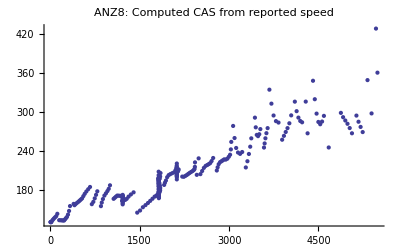

```mathematica
ListPlot[c2, PlotLabel->"ANZ8:  Computed CAS from reported speed"]
```

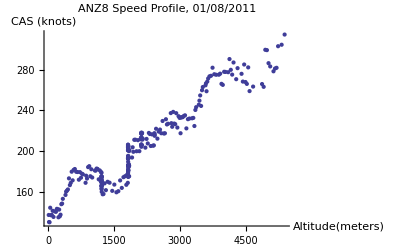

```mathematica
ListPlot[speeds99,AxesLabel->{"Altitude(meters)", "CAS (knots)"},PlotLabel->"ANZ8 Speed Profile, 01/08/2011"]
```

```mathematica
fn6
```

{{7,06/20/2009},{8,06/21/2009},{11,06/24/2009},{15,06/28/2009},{19,07/02/2009},{20,07/03/2009},{25,07/08/2009}}

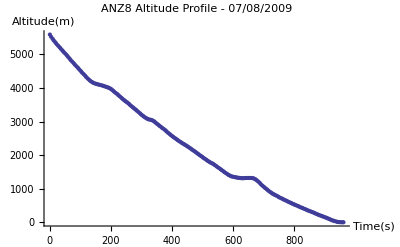

```mathematica
nztimealtprofile[fn6[[7,1]], fn6[[7,2]]]
```

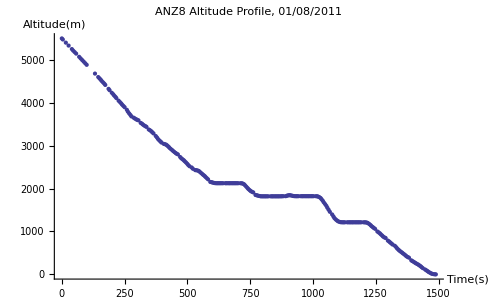

```mathematica
ListPlot[Table[{filterednzflights[[99,i,5]],filterednzflights[[99,i,3]]},{i,21, Length[filterednzflights[[99]]]}],PlotLabel->"ANZ8 Altitude Profile, 01/08/2011", AxesLabel->{"Time(s)", "Altitude(m)"}]
```

```mathematica
(* Export["waypoints.xls", waypointtabledist];*)
```

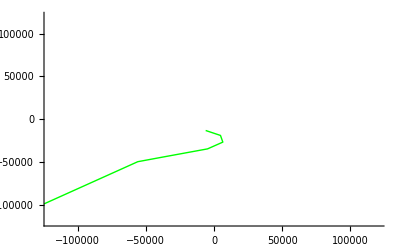

```mathematica
approach=ListPlot[Table[Take[waypointtabledist[[i]],-2],{i,1,8}],PlotRange->{{-120000,120000},{-120000,120000}},Joined->True,PlotStyle->{Green,Thick}]
```

Main

Dates for a day from each month for an SFO sample

```mathematica
dates={"20110114.lt6","20110208.lt6","20110314.lt6","20110424.lt6","20110504.lt6", "20090615.lt6","20090713.lt6","20090816.lt6","20090910.lt6","20101007.lt6","20101123.lt6","20101220.lt6"}
```

{20110114.lt6,20110208.lt6,20110314.lt6,20110424.lt6,20110504.lt6,20090615.lt6,20090713.lt6,20090816.lt6,20090910.lt6,20101007.lt6,20101123.lt6,20101220.lt6}

```mathematica
sfodaysampleindices=Sort[Table[Position[sfoanomsdays,dates[[i]]][[1,1]],{i,12}]]
```

{2,30,64,89,93,94,119,145,170,204,245,255}

```mathematica
Table[sfoanomsdays[[sfodaysampleindices[[i]]]],{i,12}]
```

{20090615.lt6,20090713.lt6,20090816.lt6,20090910.lt6,20101007.lt6,20101123.lt6,20101220.lt6,20110114.lt6,20110208.lt6,20110314.lt6,20110424.lt6,20110504.lt6}

Code to create the SFO Year

```mathematica
(* 
sfoyear={};
Do[
{
data = Import[sfoanomsdays[[sfodaysampleindices[[i]]]],"CSV"];
Print[sfoanomsdays[[sfodaysampleindices[[i]]]]],
rsi=recordstartindices[data]; (* Find out where each track record begins *)
lrsi=Length[rsi]; (* Total number of tracks in a dataset *)
parsedfulldata=Table[0,{lrsi}];(* Array to store flights *)

Do[ (* Create parsed data array, one element per flight *)
parsedfulldata[[j]]=Take[data,{rsi[[j]],rsi[[j+1]]-1}],
{j,1,lrsi-1} (* Load in all but the last one *)
];

parsedfulldata[[lrsi]]=Take[data,{rsi[[lrsi]],-1}]; (* Get the last one *)
sfoarrivals = Table[0, {lrsi}];(* Array to store subset of flights that arrive at SFO *)

Do[
sfoarrivals[[k]]=If[parsedfulldata[[k,6,1]]=="SFO" && parsedfulldata[[k,12,1]]=="A" && parsedfulldata[[k,10,1]]=="J", parsedfulldata[[k]],0],(* Filter for arrivals at SFO *)
{k,lrsi}
];
sfoarrivals=DeleteCases[sfoarrivals,0];

AppendTo[sfoyear,sfoarrivals]
},
{i,12}
]
*)
```

```mathematica
Dimensions[sfoyear]
```

{12}

```mathematica
sfy=Flatten[sfoyear,1];
```

```mathematica
Dimensions[sfy]
```

{4249}

```mathematica
(* sfy>>sfo12daysflights; *)
```

```mathematica
Dimensions[sfoyear[[2]]]
```

{386}

Pick out all of the ANZ flights from the SFO ANOMS data

```mathematica
nzflights = {};
Do[
ss = 0;
rs = 0;
{
data=Import[sfoanomsdays[[j]], "CSV"];
Print[sfoanomsdays[[j]]],
Print["datalength = ", Length[data]],
rs = recordstartindices[data];
ss = stringselect[data, "ANZ",rs];

If[
Length[ss]≥1, (* If selections are not the empty set *)

Do[
{
newaddition = Take[data, {rs[[ss[[i]]]], rs[[ss[[i]]+1]]-1}],
Print["Length[ss] = ",Length[ss]],
Print["rs[[ss[[",i,"]]]] = ",rs[[ss[[i]]]]],
AppendTo[nzflights,newaddition]   (* Pick out and add record from data *)
},{i, Length[ss]}
]

];
Print[j],
(*Clear[data]*)
}, {j,139,139}
]//Timing
```

20110108.lt6

datalength = 393289

Length[ss] = 2

rs[[ss[[1]]]] = 89045

Length[ss] = 2

rs[[ss[[2]]]] = 350088

139

{9.40263,Null}

```mathematica
interferecandidates = Table[Take[data,{rs[[i]],rs[[i+1]]-1}],{i,380,448,1}];
```

```mathematica
Take[data, {89045,89065}]
```

{{TRACK 21574568},{10831672},{01/08/2011},{09:52:18},{10:17:07},{SFO},{ANZ8},{AIR NEW ZEALAND LTD},{B772},{J},{260},{A},{SFO},{AKL},{28R},{9},{18015},{1774},{384740},{278},{-111891,-35105,5491,246,0}}

Filter for departing flights from SFO that might have interfered with the arriving ANZ flight of interest.

```mathematica
interferes=DeleteCases[Table[If[interferecandidates[[i,12,1]]=="D" && interferecandidates[[i,6,1]]=="SFO", interferecandidates[[i]],0],{i,Length[interferecandidates]}],0];
```

```mathematica
Length[interferes]
```

16

```mathematica
sfoairport
```

{37.6189,122.375}

```mathematica
interferes[[1,21,2]]
```

263

```mathematica
interfereslatlong = interferes;
```

```mathematica
Do[
{interfereslatlong[[i,j,1]]=meterstolong[interferes[[i,j,1]],0,37.6189, 122.375];
interfereslatlong[[i,j,2]]= meterstolat[interferes[[i,j,2]],0,37.6189]
},{i,16},{j,21, Length[interfereslatlong[[i]]]}
]
```

```mathematica
(* Export["Possible Conflict Departures.xls", interfereslatlong]; *)
```

```mathematica
sfoanomsdays[[139]]
```

20110108.lt6

Preparatory definitions

```mathematica
nzdistances = Table[distance[filterednzflights[[i]]],{i,188}];
```

```mathematica
group1 = distancefilter[120000,145000];
group2 = distancefilter[145000,160000];
group3 = distancefilter[160000,180000];
group4 = distancefilter[180000,210000];
groupall=distancefilter[100000,400000];
ricklist1={2,5,10,14,15,16,17,19,24,25,27,28,29,38,40,49,56,57,59};
ricklist2 ={3,8,18,20,21,22,23,33,36,50,51,52,54};
ricklist3={1,4,12,13,31,32,34,35,44,53,58};
ricklist4={7,9,22,28};
ricklist5 = {2,3,5,8,10,11,15};
fn1=filenumbers[ricklist1,group1];
fn2 = filenumbers[ricklist2,group1];
fn3 = filenumbers[ricklist3,group1];
fn4 = filenumbers[ricklist4, group3];
fn5  = filenumbers[Table[i,{i,1,188}],groupall];
fn6 = filenumbers[ricklist5, group1];
runway = Point[{-12994,-9545}];
```

```mathematica
fn6
```

{{7,06/20/2009},{8,06/21/2009},{11,06/24/2009},{15,06/28/2009},{19,07/02/2009},{20,07/03/2009},{25,07/08/2009}}

The grand loop to go through all of the data file and make movies of ANZ approaches

```mathematica
makemovies[indexlist_,destfilename_,fileno_]:=
{
Do[
ss = 0;
rs = 0;
{
data=Import[sfoanomsdays[[indexlist[[j,1]]]], "CSV"];
Print[sfoanomsdays[[indexlist[[j,1]]]]],
Print["datalength = ", Length[data]],
rs = recordstartindices[data];
ss = stringselect[data, "ANZ",rs];

If[
Length[ss]≥1, (* If selections are not the empty set *)

Do[
{
newaddition = Take[data, {rs[[ss[[i]]]], rs[[ss[[i]]+1]]-1}]
},{i, Length[ss]}
]
Print["Length[ss] = ",Length[ss]];
];

Print["j = ",j];
(* Benchmark landing time of flight of interest *)
nzlandtime = AbsoluteTime[StringJoin[Take[data, {rs[[ss[[1]]]]+2}][[1,1]],"/",Take[data, {rs[[ss[[1]]]]+4}][[1,1]]]];
 
(*Go back in time to find close flights*)
beforeindices = {};
numflightsbefore = 1;
deltat = 0;
While[deltat ≤600, 
{fr = Take[data,{rs[[ss[[1]]-numflightsbefore]],
rs[[ss[[1]]-numflightsbefore+1]]-1}];
If[
trackcandidate[fr]==True,
{
time = AbsoluteTime[StringJoin[fr[[3,1]],"/",fr[[5,1]]]],
(* Landing time *)
deltat=nzlandtime-time,
AppendTo[beforeindices,ss[[1]]-numflightsbefore]
}
]
};
 numflightsbefore++
];

(* Go forward in time to find proximal flights *)
afterindices = {};
numflightsafter = 1;
deltat = 0;
While[deltat ≤450,
{fr = Take[data,{rs[[ss[[1]]+numflightsafter]],
rs[[ss[[1]]+numflightsafter+1]]-1}];
If[
trackcandidate[fr]==True,
{
time = AbsoluteTime[StringJoin[fr[[3,1]],"/",fr[[5,1]]]]; (* Landing time *)
deltat=time-nzlandtime;
AppendTo[afterindices,ss[[1]]+numflightsafter]
}
]
};
 numflightsafter++
];

ixlist = Join[{ss[[1]]},beforeindices,afterindices];
  (* Assemble the flights that are proximal in time to the flight we're interested in, both forward and backward, plus the target flight *)
localnames = Flatten[Table[Take[data,{rs[[ixlist[[i]]]]+6}][[1]],{i,Length[ixlist]}],1]; 

locals=Table[interpolated[Take[data,{rs[[ixlist[[i]]]],rs[[ixlist[[i]]+1]]-1}]][[1]],{i,Length[ixlist]}]; (* The grand table of proximal flights, with headers stripped off, leaving only trajectory data *)

(*  If the data has its origin in the wrong place,       shift it.  Some of the data is centered around SFO, some around OAK.  Define origin as OAK *)

Do[
If[
Abs[locals[[i,-1,1]]]<2000, 
locals[[i,j]]=
{
locals[[i,j,1]]-12994,
locals[[i,j,2]]-9545,
locals[[i,j,3]],
locals[[i,j,4]],
locals[[i,j,5]]
};
],{i,Length[locals]},{j,1,Length[locals[[i]]]}
];

refstarttime = locals[[1,1,5]]; (* Start time for flight of interest *)
refendtime = locals[[1,-1,5]];    (* End time for flight of interest *)
earliesttime = Min[Table[locals[[i,1,5]],{i,Length[locals]}]];
(* Earliest start of any proximal flight *)
latesttime =  Max[Table[locals[[i,-1,5]],{i,Length[locals]}]];
(* Latest end of any proximal flight *)
timespread = latesttime-earliesttime;
timematrix = Table[{999999,999999}, {n, Length[locals]},{i,timespread+1}]; 
(* Use placeholder x,y values so translation to .xls works ok since
zeros generate pathologies *)

	Do
[ (* Construct the trimmed table that starts and ends with the target flight times *)
{offset= locals[[i,1,5]]-earliesttime,
Do
[
timematrix[[i,m + offset]]=Take[locals[[i,m]],2],
{m, Length[locals[[i]]]}
]
},{i,Length[locals]}
];
trimmedtimematrix = Table[timematrix[[i,k]],{i,Length[locals]},
{k,refstarttime-earliesttime+1,refendtime-earliesttime+1}]
(* Print["duration of movie = ",Length[trimmedtimematrix[[1]]]," seconds"];Print["Start frame creation of movie #", j];
frames = Table[Show[approach, showrunway,acpointplot[trimmedtimematrix,i]],{i,1,Length[trimmedtimematrix[[1]]],3}];
Print["End frame creation of movie #", j];
aviname = StringJoin[destfilename,sfoanomsdays[[indexlist[[j,1]]]],".avi"];
Export[aviname,frames];
Print["Export of file ",j," complete"];
Clear[data] *)
}, {j,fileno,fileno}
];
}//Timing
```

```mathematica
flubs = {76,81}
```

```mathematica
ixlist
```

{448,445,440,435,432,426,453,457,463,467}

```mathematica
data[[445]]
```

{22631,-12373,1107,110,617}

```mathematica
Position[filterednzflights, "01/08/2011"]
```

{{99,3,1}}

```mathematica
(* exports[datelist_]:=
{
Export[StringJoin["ArrivalGroup",ToString[datelist],".xls"], trimmedtimematrix],
Export[StringJoin["ArrivalGroupFltIDs",ToString[datelist],".xls"],localnames]
} *)
```

Rick Calculations

```mathematica
fn6
```

{{7,06/20/2009},{8,06/21/2009},{11,06/24/2009},{15,06/28/2009},{19,07/02/2009},{20,07/03/2009},{25,07/08/2009}}

```mathematica
distanceabovealtitude[filterednzflights[[99]], 3068]
```

73265

```mathematica
pydistanceabovealtitude[filterednzflights[[99]], 3068]//N
```

69009.1

```mathematica
pydistancebetweenaltitude[filterednzflights[[11]],5000, 3068]//N
```

48497.6

```mathematica
levelflightbetweenaltitude[filterednzflights[[99]],3069,1000]//N
```

410.

```mathematica
pydistanceabovealtitude[locals[[2]],3068]//N
```

63815.6

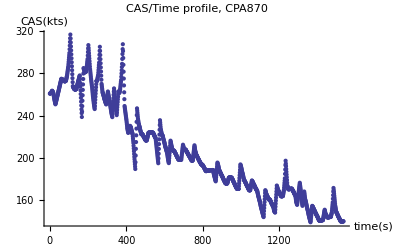

```mathematica
ListPlot[Table[locals[[2,i,4]] 1.944 *Sqrt[densitylowratio[locals[[2,i,3]]]],{i,Length[locals[[2]]]}],PlotLabel->"CAS/Time profile, CPA870", AxesLabel->{"time(s)", "CAS(kts)"}]
```

```mathematica
interplanedistances = DeleteCases[Table[
If
[trimmedtimematrix[[2,i,1]]≠999999, Sqrt[(trimmedtimematrix[[1,i,1]]-trimmedtimematrix[[2,i,1]])^2+
(trimmedtimematrix[[1,i,2]]-trimmedtimematrix[[2,i,2]])^2],0
],{i,Length[trimmedtimematrix[[1]]]}
],0]//N;
```

```mathematica
(* Export["InterplaneDistance ANZ8 CPA870.xls", interplanedistances]; *)
```

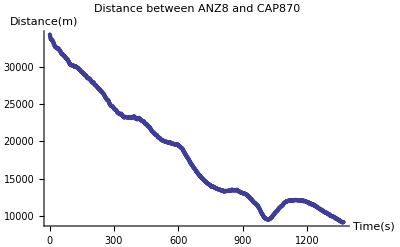

```mathematica
ListPlot[interplanedistances,PlotLabel->"Distance between ANZ8 and CAP870", AxesLabel->{"Time(s)", "Distance(m)"}]
```

```mathematica
exports[20110108]
```

{ArrivalGroup20110108.xls,ArrivalGroupFltIDs20110108.xls}

```mathematica
runway
```

Point[{-12994,-9545}]

```mathematica
sfoairport
```

{37.6189,122.375}

Convert the coordinates of the aircraft locations to lat/long using a tangent plane approximation.

```mathematica
latlongtable=Table[{meterstolong[trimmedtimematrix[[i,j,1]],-12994,37.6189,122.375],
meterstolat[trimmedtimematrix[[i,j,2]], -9545, 37.6189]},{i,Dimensions[trimmedtimematrix][[1]]},{j,Dimensions[trimmedtimematrix][[2]]}];
```

```mathematica
(* Export["20110108LatLong.xls", latlongtable]; *)
```

```mathematica
makemovies[fn6,"Rick ANZ Movies",1]
```

20090620.lt6

datalength = 645372

Length[ss] = 2

j = 1

{13.4283,{Null}}

```mathematica
Take[filterednzflights[[99]],24]
```

{{TRACK 21574568},{10831672},{01/08/2011},{09:52:18},{10:17:07},{SFO},{ANZ8},{AIR NEW ZEALAND LTD},{B772},{J},{260},{A},{SFO},{AKL},{28R},{9},{18015},{1774},{384740},{278},{-124885,-44650,5491,246,0},{-123719,-44730,5466,292,4},{-121298,-44688,5392,202,16},{-118715,-44920,5324,236,27}}

```mathematica
48498/278.
```

174.453

```mathematica
51141/294.
```

173.949

```mathematica
56885/306.
```

185.899

```mathematica
52572/280.
```

```mathematica
48517/272.
```

178.371

```mathematica
localnames
```

{ANZ8,CPA870,UAL857,KAL023,SKW6616,SKW4611,UAL556,AWE403,SKW6673,OPT846}

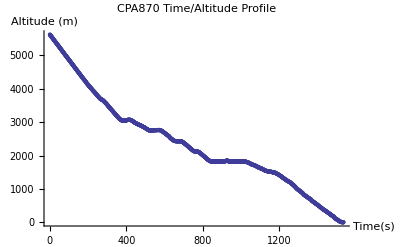

```mathematica
ListPlot[Table[locals[[2,j,3]],{j,Length[locals[[2]]]}],PlotLabel->"CPA870 Time/Altitude Profile", AxesLabel->{"Time(s)", "Altitude (m)"}]
```

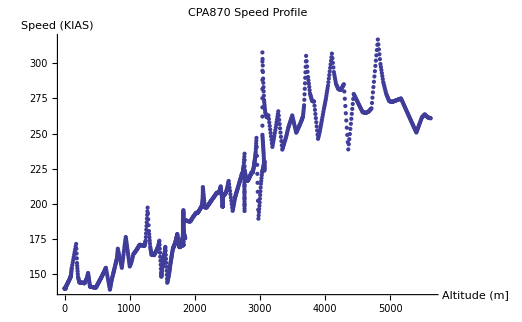

```mathematica
ListPlot[Table[{locals[[2,j,3]],1.944 Sqrt[densitylowratio[locals[[2,j,3]]]]*locals[[2,j,4]]},{j,Length[locals[[2]]]}],PlotLabel->"CPA870 Speed Profile", AxesLabel->{"Altitude (m]","Speed (KIAS)"}]
```

```mathematica
locals[[3,-1]]
```

{-12549,-9564,3,61,3503470383}

```mathematica
locals[[1]]
```

```mathematica
localnames
```

{ANZ8,CPA870,UAL857,KAL023,SKW6616,SKW4611,UAL556,AWE403,SKW6673,OPT846}

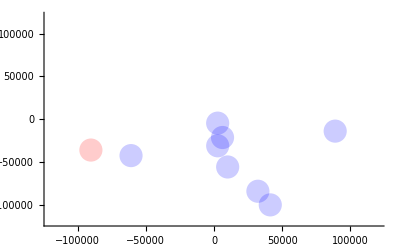

```mathematica
va=acpointplot[trimmedtimematrix,110]
```

```mathematica
showrunway = Graphics[{PointSize[.03],Red,runway}];
```

```mathematica
frames = Table[Show[approach, showrunway,acpointplot[trimmedtimematrix,i]],{i,1,Length[trimmedtimematrix[[1]]],3}];
```

```mathematica
ListAnimate[Table[Show[approach, showrunway,acpointplot[trimmedtimematrix,i]],{i,1,Length[trimmedtimematrix[[1]]],3}]]
```

```mathematica
nzflights=<<nzflights;
```

```mathematica
Length[nzflights]
```

426

```mathematica
(*  Isolate the flights that could be ANZ tailored arrivals *)filterednzflights=DeleteCases[Table[If[StringMatchQ[nzflights[[i,12]][[1]],"A"]==True && (StringMatchQ[nzflights[[i,15]],"28R"][[1]]==True || 
StringMatchQ[nzflights[[i,15]],"28L"][[1]]==True), nzflights[[i]],0],{i,3, Length[nzflights]}],0];
```

```mathematica
filterednzflights=<<filterednzflights;
```

```mathematica
Dimensions[filterednzflights]
```

{188}

```mathematica
distancefrompirat[nztano_]:=
{
distances=Table[{Abs[Sqrt[(filterednzflights[[nztano,j,1]]-waypointtabledist[[2,2]])^2+
(filterednzflights[[nztano,j,2]]-waypointtabledist[[2,3]])^2]-9 1852],j},{j,21,Length[filterednzflights[[nztano]]]}];
minlist = {};Do[If[distances[[k+1,1]]>distances[[k,1]]&&distances[[k-1,1]]>distances[[k,1]]&&distances[[k,1]]<1500, AppendTo[minlist,k]],{k,2,Length[distances]-1}];
minlist
}
```

```mathematica
distancefromnepic[nztano_]:=
{
distances=Table[{Abs[Sqrt[(filterednzflights[[nztano,j,1]]-waypointtabledist[[8,2]])^2+
(filterednzflights[[nztano,j,2]]-waypointtabledist[[8,3]])^2]-0.5 1852],j},{j,21,Length[filterednzflights[[nztano]]]}];
minlist = {};Do[If[distances[[k+1,1]]>distances[[k,1]]&&distances[[k-1,1]]>distances[[k,1]]&&distances[[k,1]]<500, AppendTo[minlist,k]],{k,2,Length[distances]-1}];
minlist
}
```

```mathematica
pirat9nmindices = Table[distancefrompirat[i][[1,1]]+20,{i,188}]
```

{42,95,41,42,44,43,42,43,42,39,45,57,44,45,41,43,45,40,40,42,39,43,42,42,44,42,42,41,42,40,50,43,41,42,42,44,43,49,44,41,43,44,42,37,44,41,44,42,35,43,23,44,42,43,42,43,42,43,41,40,40,44,42,42,45,45,43,59,63,49,58,52,52,60,53,54,58,60,53,49,49,58,51,62,47,60,50,42,59,63,53,55,59,61,41,59,56,75,61,51,47,49,50,52,59,58,44,57,52,51,53,50,56,63,55,53,65,60,51,37,55,59,54,61,56,56,52,54,55,54,35,51,56,53,51,42,57,55,59,60,51,45,35,41,38,55,54,46,60,49,60,52,56,53,65,37,60,64,94,58,40,59,57,41,59,56,60,59,54,50,68,57,55,56,53,56,57,55,38,60,60,81,49,53,57,55,61,41}

```mathematica
nepicohthreenmindices = Table[distancefromnepic[i][[1,-2]]+20,{i,188}]
```

Part::partw: Part -2 of {} does not exist.

{668,368,227,208,224,251,211,222,232,198,228,300,209,209,235,210,211,198,268,203,197,200,206,198,202,206,211,197,203,239,273,203,271,196,208,234,244,345,389,239,208,242,235,202,199,217,210,222,199,273,227,222,214,226,200,201,221,202,364,195,198,388,196,200,249,232,319,220,223,199,257,207,237,231,198,281,222,232,262,218,191,257,197,216,223,269,201,191,408,237,211,210,234,217,188,215,208,254,276,234,219,188,226,370,256,208,452,254,208,255,208,198,207,218,224,204,218,205,260,205,462,217,213,222,205,218,235,217,215,223,186,224,203,237,218,490,245,205,215,217,238,285,20+{{}}⟦1,-2⟧,128,166,231,200,220,269,489,237,192,216,210,312,230,220,293,305,260,244,257,230,207,213,211,209,220,216,223,217,219,209,218,249,250,263,217,457,215,202,332,233,238,231,215,237,221}

```mathematica
piratnepictimes = Join[Table[filterednzflights[[i,nepicohthreenmindices[[i]],5]]-filterednzflights[[i,pirat9nmindices[[i]],5]],{i,142}],
Table[filterednzflights[[i,nepicohthreenmindices[[i]],5]]-filterednzflights[[i,pirat9nmindices[[i]],5]],{i,144,188}]]
```

{2914,1261,859,767,830,959,781,826,877,735,850,1122,762,757,896,772,767,729,1058,743,730,725,757,720,730,757,780,720,743,919,1030,738,1062,710,767,877,928,1367,1601,917,763,915,899,761,715,814,766,831,757,1062,941,822,794,846,730,729,826,757,1491,715,729,1588,716,729,942,862,1275,818,831,761,1018,791,948,880,749,1171,836,877,1080,848,726,1012,741,796,899,1089,782,751,1768,888,810,799,897,799,753,803,785,920,1091,939,882,723,902,1602,996,769,2203,1007,805,1039,803,761,773,789,864,765,779,749,1062,861,2223,802,807,831,769,817,938,844,825,857,775,892,757,937,857,2427,957,775,802,824,958,1213,786,768,895,746,889,1060,2298,898,731,794,759,1186,910,756,1090,1013,1035,1034,1015,888,774,724,724,726,756,777,825,735,922,754,792,934,921,981,761,2074,720,695,1200,879,855,835,786,826,845}

```mathematica
piratnepicdistances = Join[Table[Sum[Sqrt[(filterednzflights[[i,j,1]]-filterednzflights[[i,j+1,1]])^2 + (filterednzflights[[i,j,2]]-filterednzflights[[i,j+1,2]])^2],
{j,pirat9nmindices[[i]],nepicohthreenmindices[[i]]-1}],{i,142}]//N,
Table[Sum[Sqrt[(filterednzflights[[i,j,1]]-filterednzflights[[i,j+1,1]])^2 + (filterednzflights[[i,j,2]]-filterednzflights[[i,j+1,2]])^2],
{j,pirat9nmindices[[i]],nepicohthreenmindices[[i]]-1}],{i,144,188}]//N]
```

```mathematica
dates=Join[Table[filterednzflights[[i,3,1]],{i,142}],Table[filterednzflights[[i,3,1]],{i,144,188}]]
```

```mathematica
ricknzpathdata=Table[{dates[[i]],piratnepicdistances[[i]],piratnepictimes[[i]]},{i,187}];
```

```mathematica
(* Export["NZPathData.XLS", ricknzpathdata]; *)
```

```mathematica
Histogram[piratnepicdistances,80, PlotRange->{{90000,200000},{0,50}},PlotLabel->"ANZ SFO PIRAT/NEPIC Traversal Distances, 187 Flights",AxesLabel->{"Distance(m)", "Number of Flights"}]
```

-Graphics-

```mathematica
Histogram[piratnepictimes,50,PlotRange->{{600,2000},{0,50}},PlotLabel->"ANZ SFO PIRAT/NEPIC Traversal Times, 187 Flights",AxesLabel->{"Time(s)", "Number of Flights"}]
```

-Graphics-

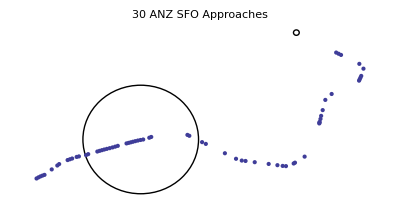

```mathematica
tableofplots=Table[ListPlot[Table[{filterednzflights[[i,j,1]],filterednzflights[[i,j,2]]},{j,21, Length[filterednzflights[[i]]]}]],{i,143,143}];
piratcircle = Graphics[Circle[{waypointtabledist[[2,2]],waypointtabledist[[2,3]]},10 1852]];
Show[{piratcircle,tableofplots}, PlotLabel->"30 ANZ SFO Approaches"];
nepiccircle = Graphics[Circle[{waypointtabledist[[8,2]],waypointtabledist[[8,3]]},.5 1852]];
Show[{piratcircle,nepiccircle,tableofplots}, PlotLabel->"30 ANZ SFO Approaches"]
```

```mathematica
Histogram[nzdistances,60, PlotLabel->"Terminal Airspace Track Distance, 188 ANZ7 arrivals", AxesLabel->{"meters", "number"},PlotRange->{{100000,400000},{0,30}}]
```

-Graphics-

Rick groupings  are 120-145km, 145-160km, 160-180km, 180-210km.

```mathematica
nzdurations = Table[universaltime[filterednzflights[[i,3]],filterednzflights[[i,5]]]-
universaltime[filterednzflights[[i,3]],filterednzflights[[i,4]]],{i,188}];
```

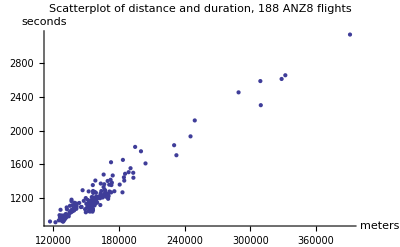

```mathematica
ListPlot[Table[{nzdistances[[i]],nzdurations[[i]]},{i,188}],PlotLabel->"Scatterplot of distance and duration, 188 ANZ8 flights", AxesLabel->{"meters","seconds"}]
```

```mathematica
Histogram[nzdurations,50,PlotRange->{{500,3300},{0,30}},PlotLabel->"Terminal Airspace Residency of ANZ8, 188 Arrivals", AxesLabel->{"sec", "number"}]
```

-Graphics-

```mathematica
(* Check to see what flight numbers the ANZ arrivals have *)Table[filterednzflights[[i,7]],{i,188}];
```

```mathematica
filterednzflights=<<filterednzflights;
```

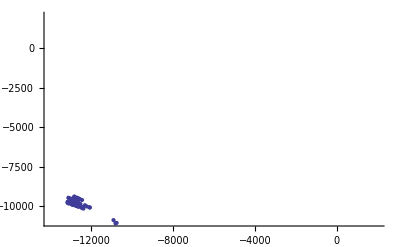

```mathematica
(*  There seems to be a coordinate redefinition during data acquisition *)endpoints = Table[Take[filterednzflights[[i,-1]],2],{i,188}];
ListPlot[endpoints,PlotRange->{{-14000, 2000},{-11000,2000}}]
```

```mathematica
correctednzflights=filterednzflights;
(*  Modify copy of filterednzflights to account for change of coordinate
system during data collection years *)
Do[
If[
Abs[filterednzflights[[i,-1,1]]]<2000, 
correctednzflights[[i,j]]=
{
filterednzflights[[i,j,1]]-12994,
filterednzflights[[i,j,2]]-9545, 
filterednzflights[[i,j,3]],
filterednzflights[[i,j,4]],
filterednzflights[[i,j,5]]
}
],{i,188},{j,21,Length[filterednzflights[[i]]]}
];
```

```mathematica
correctednzflights>>filterednzflights;
```

```mathematica
(* Export["nzarrivals.xls",correctednzflights]; *)
```

```mathematica
tableofpoints[groupindices_]:=
Table[correctednzflights[[groupindices[[i]]]],{i,Length[groupindices]}];
```

```mathematica
set4=tableofpoints[group4];
```

```mathematica
(* Export["group4.xls", set4]; *)
```

```mathematica
Length[Flatten[set4,1]]
```

3949

```mathematica
tableofplots[groupindices_]:=Show[Table[ListPlot[Table[{correctednzflights[[groupindices[[i]],j,1]],correctednzflights[[groupindices[[i]],j,2]]},{j,21, Length[correctednzflights[[groupindices[[i]]]]]}]],{i,Length[groupindices]}]]
```

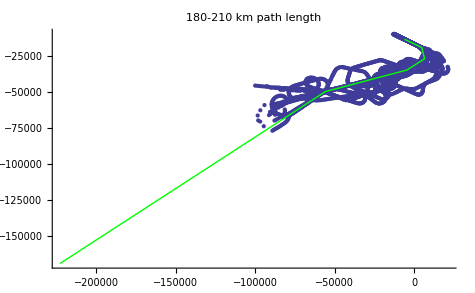

```mathematica
Show[tableofplots[group4],approach,PlotLabel->"180-210 km path length"]
```

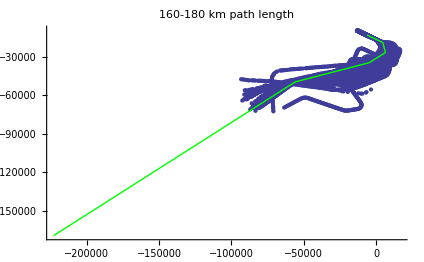

```mathematica
Show[tableofplots[group3],approach,PlotLabel->"160-180 km path length"]
```

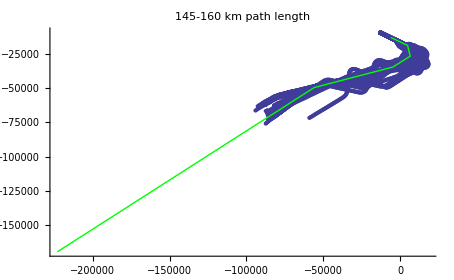

```mathematica
Show[tableofplots[group2],approach,PlotLabel->"145-160 km path length"]
```

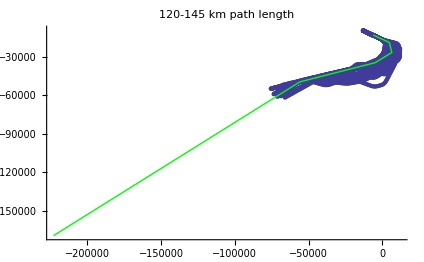

```mathematica
Show[tableofplots[group1],approach,PlotLabel->"120-145 km path length"]
```

```mathematica
tableofplots=Table[ListPlot[Table[{filterednzflights[[i,j,1]],filterednzflights[[i,j,2]]},{j,21, Length[filterednzflights[[i]]]}]],{i,188}];
```

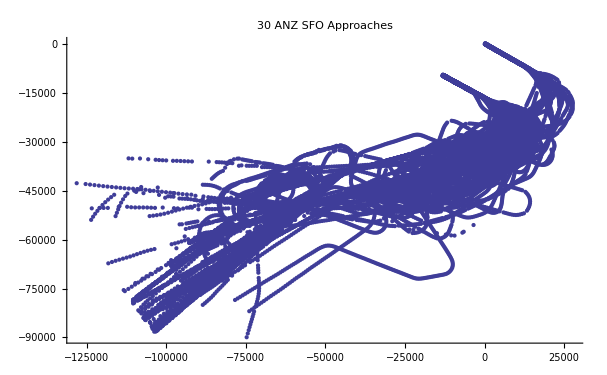

```mathematica
Show[tableofplots, PlotLabel->"30 ANZ SFO Approaches"]
```

```mathematica
nzflights = Take[nzflights, {1, 254}];
```

```mathematica
nzflights>>nzflights;
```

```mathematica
nzflatanalysis[nzflightdata_,deltahthreshold_,altthreshold_]:=
{
flat = 0;
Do
[
If[nzflightdata[[i,3]]>altthreshold && nzflightdata[[i,3]]-nzflightdata[[i+1,3]]≤deltahthreshold, flat = flat + nzflightdata[[i+1,5]]-nzflightdata[[i,5]]], 
{i, 21,Length[nzflightdata]-1}
];
flat}[[1]]
```

```mathematica
nzflatanalysisfeet[nzflightdata_,deltahthreshold_,altlowerboundft_,altupperboundft_]:=
{
flat = 0;
Do
[
If[3.2808nzflightdata[[i,3]]>altlowerboundft &&3.2808 nzflightdata[[i,3]]≤altupperboundft && nzflightdata[[i,3]]-nzflightdata[[i+1,3]]≤deltahthreshold, flat = flat + Sqrt[(nzflightdata[[i+1,1]]-nzflightdata[[i,1]])^2+
(nzflightdata[[i+1,2]]-nzflightdata[[i,2]])^2]/1944.], 
{i, 21,Length[nzflightdata]-1}
];
If[flat≥3.0,flat,0]
}[[1]]
```

```mathematica
nzflats = Table[nzflatanalysisfeet[filterednzflights[[i]], 10,4500+ 1000 j,5500+1000 j],{i,188},{j,23}];
```

```mathematica
Plus@@Flatten[nzflats]
```

2233.06

```mathematica
Prepend[{2,3},1,2]
```

Prepend::argrx: Prepend called with 3 arguments; 2 arguments are expected.

Prepend[{2,3},1,2]

```mathematica
nzflatsout=nzflats;
```

```mathematica
Do[nzflatsout[[i]]=Flatten[Join[{i,filterednzflights[[i,3]][[1]],nzflats[[i]]}]],{i,2}]
```

```mathematica
nzflatsout[[2]]
```

{2,06/17/2009,12.6842,8.70397,0,0,10.4216,0,0,0,0,0,17.5675,0,0,0,0,0,0,0,0,0,0,0,0}

```mathematica
fbtable=<<fbtable;
```

```mathematica
nzflats[[1,1]]
```

1

```mathematica
Dimensions[nzflats]
```

{188,23}

```mathematica
fbtable
```

{{6000,22.516},{7000,22.2937},{8000,22.0731},{9000,21.8544},{10000,21.6375},{11000,22.6757},{12000,22.4659},{13000,22.2579},{14000,22.0517},{15000,21.8472},{16000,21.6445},{17000,21.4435},{18000,21.2443},{19000,21.0469},{20000,20.8512},{21000,20.6572},{22000,20.465},{23000,20.2745},{24000,20.0858},{25000,19.8988},{26000,19.7136},{27000,19.5301},{28000,19.3484}}

```mathematica
nzflatsfb = Table[If[j ≠5, nzflats[[i,j]],If[nzflats[[i,j]]-8033./1944.≥0,nzflats[[i,j]]-8033./1944.,0]] fbtable[[j,2]],{i,188},{j,23}];
```

```mathematica
leveldistfuel = Table[{nzflats[[i,j]],nzflatsfb[[i,j]]},{i,188},{j,23}];
```

```mathematica
Plus@@Flatten[nzflatsfb]
```

45762.5

```mathematica
nzlevelout=leveldistfuel;
```

```mathematica
Do[nzlevelout[[i]]=Prepend[leveldistfuel[[i]],filterednzflights[[i,3]][[1]]],{i,188}]
```

```mathematica
Do[nzlevelout[[i]]=Prepend[nzlevelout[[i]],i],{i,188}]
```

```mathematica
nzlevelout[[2]]
```

{2,06/17/2009,{12.6842,285.598},{8.70397,194.043},{0,0},{0,0},{10.4216,136.086},{0,0},{0,0},{0,0},{0,0},{0,0},{17.5675,380.239},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0},{0,0}}

```mathematica
(* Export["ANZLevelAnalysis.xls", nzlevelout]; *)
```

```mathematica
(* Export["ANZlevelflight.xls", nzflats]; *)
```

```mathematica
Take[filterednzflights[[1]],{1,3}]
```

{{TRACK 19858452},{8743194},{06/15/2009}}

```mathematica
anzdelaydataout = Table[{filterednzflights[[i,3]],nzflats[[i]]},{i,188}];
```

```mathematica
FileNames[]
```

```mathematica
(* Export["ANZflats.xls", anzdelaydataout] *)
```

ANZflats.xls

```mathematica
nzflats2 = nzflats;
```

```mathematica
longnzflats =DeleteCases[ Table[If[nzflats[[i]]≥20, nzflats[[i]],0],{i,Length[nzflats]}],0]
```

{226,545,818,142,28,23,28,145,162,140,27,158,143,28,92,23,105,27,138,150,129,32,23,595,204,115,143,1062,108,145}

```mathematica
Length[longnzflats]
```

30

```mathematica
Histogram[longnzflats,{0,1100,20},PlotRange->{0,10},AxesOrigin->{0,0}, PlotLabel->"ANZ8 Tailored Arrivals, High Altitude Level Flying", AxesLabel->{"seconds", "number of flights"}]
```

-Graphics-

```mathematica
test = {1,2,3,4}
```

{1,2,3,4}

{1,2,3,4}

Previous Analysis

I see it is possible to index a long list of file names because the list is an expression that can be manipulated in a standard way.

Parse the data into individual flights, separate out the trackpoints from the metadata.

```mathematica
trackmatrix=Table[{},{3088}];
startpositioncounter=1;
Do[
{
trackpoints=data[[startpositioncounter+19]][[1]];
trackmatrix[[trackindex]]=Take[data, {startpositioncounter, startpositioncounter+19+trackpoints}];
startpositioncounter=startpositioncounter+20+trackpoints
},{trackindex,  3088}
]
```

A breakout of all of the different kinds of aircraft arriving or departing SFO.

```mathematica
Sort[Tally[DeleteCases[Table[If[trackmatrix[[i,6,1]]=="SFO",trackmatrix[[i,10]],0],{i,3088}],0]], #1[[2]]>#2[[2]]&]
```

{{{J},721},{{R},162},{{T},146},{{B},66},{{H},15},{{P},6},{{U},6},{{M},1}}

Total number of aircraft using SFO

```mathematica
Plus@@Table[If[trackmatrix[[i,6,1]]=="SFO", 1],{i,3088}]
```

1123+1965 Null

Create datamatrix of track data without metadata, normalize time in seconds from 000 hrs Zulu.

```mathematica
datamatrix=Table[Take[trackmatrix[[i]],{21, Length[trackmatrix[[i]]]}], {i,1,3088}];
```

```mathematica
starttimesvector=Table[AbsoluteTime[StringJoin["01 Jan 1900"," ", trackmatrix[[i,4,1]]]],{i,3088}];
Do[
Do[
datamatrix[[i,j,5]]=datamatrix[[i,j,5]]+starttimesvector[[i]],{j,1,Length[datamatrix[[i]]]}
],{i,3088}
];
```

See how many unique seconds are represented.  If everybody is pinged at once, there should be about 1/4 or 1/5 of the seconds in a day.  If aircraft are pinged in sequence, there could be up to the number of seconds in a day, depending on where a particular aircraft is when the radar sweeps by.  The latter hypothesis seems to be true.  Aircraft are pinged by a rotating sweep that is phase distributed.

```mathematica
uniquetimes=Union[Flatten[Table[datamatrix[[i,j,5]],{i,3088},{j,Length[datamatrix[[i]]]}]]];
```

```mathematica
Length[uniquetimes]
```

73983

A filter for finding arrivals at SFO--They start at greater than 3000 meters, traveling faster than 50 m/s, end altitude less than 1000m (not actual runway elevation to allow for data dropouts), and are identified with SFO.

```mathematica
c=0;
indexlist={};
Do[
If[
(
datamatrix[[i,1,3]]≥3000
&&Mean[Table[datamatrix[[i,j,4]], {j,1,10}]]≥50
&&trackmatrix[[i,6,1]]=="SFO"
&&  Take[datamatrix[[i]],-1][[1,3]]<1000
), 
{
c++,
indexlist=Append[indexlist,i]
}], 
{i,3088}
]
Print[c]
```

529

Using trackpoints to determine differentials for speed, acceleration, etc.

```mathematica
difftable[trackmatrixelement_,windowsize_]:=diffs=Table[{Sqrt[(trackmatrixelement[[i+windowsize,1]]-trackmatrixelement[[i,1]])^2+
(trackmatrixelement[[i+windowsize,2]]-trackmatrixelement[[i,2]])^2]//N,trackmatrixelement[[i+windowsize,3]]-trackmatrixelement[[i,3]],trackmatrixelement[[i+windowsize,4]]-trackmatrixelement[[i,4]],
trackmatrixelement[[i+windowsize,5]]-trackmatrixelement[[i,5]]},{i,21,Length[trackmatrixelement]-windowsize}]
```

```mathematica
difftable[trackmatrix[[32]],5];
```

```mathematica
differentials[difftable_]:=differs=Table[{difftable[[i,1]]/difftable[[i,4]],difftable[[i,2]]/difftable[[i,4]],difftable[[i,3]]/difftable[[i,4]]},{i,Length[difftable]}]//N
```

```mathematica
differentials[diffs];
```

```mathematica
differs[[2,1]]
```

206.724

```mathematica
Length[differs]
```

157

```mathematica
trackmatrix[[32,20]]
```

{162}

The data are somewhat noisy

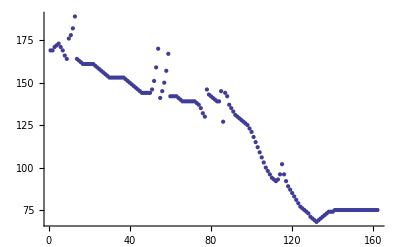

```mathematica
ListPlot[Table[trackmatrix[[35,i,4]],{i,21,182}]]
```

Airspeed is a noisy signal

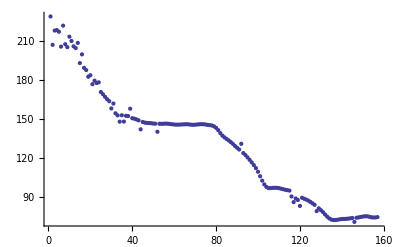

```mathematica
ListPlot[Table[differs[[i,1]],{i,Length[diffs]}]]
```

Definitely an inefficient descent profile

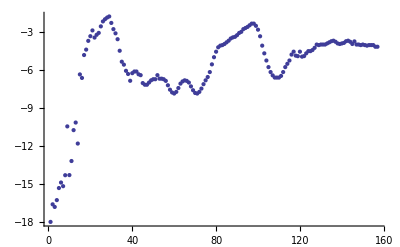

```mathematica
ListPlot[Table[differs[[i,2]],{i,Length[diffs]}]]
```

And a bumpy ride

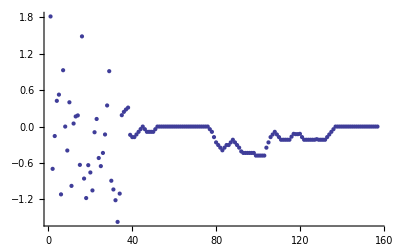

```mathematica
ListPlot[Table[differs[[i,3]],{i,Length[diffs]}]]
```

Create functions for plotting trajectory horizontal and vertical components

```mathematica
planar[index_]:=ListPlot[Table[{trackmatrix[[index,i,1]],trackmatrix[[index,i,2]]},{i,21,Length[trackmatrix[[index]]]}],AxesOrigin->{0,0},AspectRatio->1,PlotJoined->True]
```

```mathematica
vert[index_]:=ListPlot[Table[{Sqrt[(trackmatrix[[index,i,1]]+13000)^2+(trackmatrix[[index,i,2]]+9000)^2],trackmatrix[[index,i,3]]}, {i, 21, Length[trackmatrix[[index]]]}],AxesOrigin->{0,0},PlotJoined->True]
```

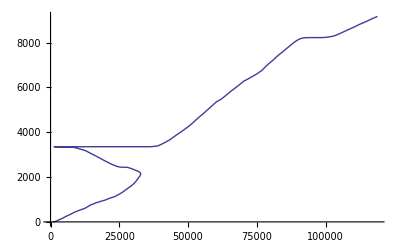

```mathematica
vert[1164]
```

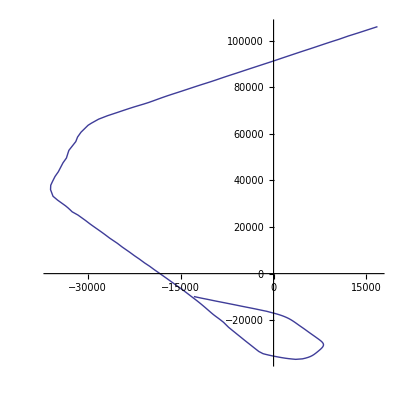

```mathematica
planar[1164]
```

Build a function that detects flat segments of a certain time duration, measured in radar pings (4.2 seconds according to Rick Shay)

```mathematica
flatdetector[dataelement_,numpings_]:=
Table[If[dataelement[[i+numpings,3]]≥dataelement[[i,3]]-25, dataelement[[i,3]],0],{i,Length[dataelement]-10}]
```

This adds the segments to each string of level flying that make up the missed width of the flatdetector[] detection window used to detect the level flying, as the flat elements are only detected after a certain number (6 in the function above, or 25.2 sec) of radar pings.

```mathematica
flatfix[index_,windowsize_]:={
edges={};
workvector=flats[[index]];

Do[
If[
workvector[[i]]≠0 && workvector[[i+1]]==0, 
edges=Append[edges,i]
],{i,1,Length[workvector]-1}
];

Do[
workvector[[edges[[k]]+m]]=datamatrix[[indexlist[[index]],edges[[k]]+m,3]],{k,Length[edges]},{m,windowsize}
];
};
```

```mathematica
flats=Table[flatdetector[datamatrix[[indexlist[[i]]]],6],{i,Length[indexlist]}];
```

```mathematica
levelsegs=flats;
Do[
{
flatfix[i,6],
levelsegs[[i]]=workvector
},{i,529}
]
```

```mathematica
purelevel3=Flatten[Table[DeleteCases[levelsegs[[i]],0], {i, 529}]];
```

```mathematica
Length[purelevel3]
```

15034

Level Flight Fuel Burn Analysis

```mathematica
swa=DeleteCases[Table[If[trackmatrix[[indexlist[[flatties[[i]]]],8,1]]=="SOUTHWEST AIRLINES CO",i,0],{i,74}],0]
```

{15,31,41,47,67}

```mathematica
united=DeleteCases[Table[If[trackmatrix[[indexlist[[flatties[[i]]]],8,1]]=="UNITED AIR LINES INC",i,0],{i,74}],0]
```

{8,10,19,34,35,36,43,55,56}

```mathematica
skywest=DeleteCases[Table[If[trackmatrix[[indexlist[[flatties[[i]]]],8,1]]=="SKY WEST AVIATION INC TRUSTEE",i,0],{i,74}],0]
```

{1,2,3,4,5,6,9,11,13,14,16,18,20,22,26,29,32,33,39,40,42,44,45,46,48,50,58,60,61,62,64,65,68,70,72}

```mathematica
delta=DeleteCases[Table[If[trackmatrix[[indexlist[[flatties[[i]]]],8,1]]=="DELTA AIR LINES INC",i,0],{i,74}],0]
```

{17,37,66,73}

```mathematica
sumsky=0;
Do[
{
trackflats=levelsegs[[flatties[[skywest[[i]]]]]];
sumsky+=Sum[If[trackflats[[j]]>3500, 4.2 crj200fburn[trackflats[[j]]],0],{j,Length[trackflats]}]
},
{i,Length[skywest]}
]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power will be suppressed during this calculation.

```mathematica
sumsky
```

1131.78

```mathematica
sumsky=0;
Do[
{
trackflats=levelsegs[[flatties[[united[[i]]]]]];
sumsky+=Sum[If[trackflats[[j]]>3500, 4.2 a320fburn[trackflats[[j]]],0],{j,Length[trackflats]}]
},
{i,Length[united]}
]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power will be suppressed during this calculation.

```mathematica
2.20462 132
```

291.01

```mathematica
sumsky
```

468.564

```mathematica
sumsky=0;
Do[
{
trackflats=levelsegs[[flatties[[delta[[i]]]]]];
sumsky+=Sum[If[trackflats[[j]]>3500, 4.2 a320fburn[trackflats[[j]]],0],{j,Length[trackflats]}]
},
{i,Length[delta]}
]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power will be suppressed during this calculation.

```mathematica
sumsky
```

131.822

```mathematica
sumsky=0;
Do[
{
trackflats=levelsegs[[flatties[[swa[[i]]]]]];
sumsky+=Sum[If[trackflats[[j]]>3500, 4.2 a320fburn[trackflats[[j]]],0],{j,Length[trackflats]}]
},
{i,Length[swa]}
]
```

Power::infy: Infinite expression 1/0 encountered.

General::stop: Further output of Power will be suppressed during this calculation.

```mathematica
sumsky 2.20462
```

467.737

```mathematica
uniqueaircraftpicker=Table[If[levelsegs[[i,j]]>=3500,i,0],{i,529},{j,Length[levelsegs[[i]]]}];
```

```mathematica
flatties=DeleteCases[Union[Flatten[uniqueaircraftpicker]],0]
```

{10,11,13,17,21,30,34,37,58,64,65,79,97,119,120,132,148,151,154,162,167,178,180,186,187,188,191,196,197,200,202,206,217,221,225,227,230,235,238,244,245,260,262,263,264,265,269,273,277,282,307,311,321,324,340,342,345,348,350,352,358,368,378,379,382,388,407,433,435,474,497,513,515,519}

```mathematica
Length[flatties]
```

74

```mathematica
Tally[Table[trackmatrix[[indexlist[[flatties[[i]]]],8]],{i,Length[flatties]}]]
```

{{{SKY WEST AVIATION INC TRUSTEE},35},{{MESABA AVIATION},2},{{UNITED AIR LINES INC},9},{{VIRGIN AMERICA},2},{{SOUTHWEST AIRLINES CO},5},{{DELTA AIR LINES INC},4},{{KLM ROYAL DUTCH AIRLINES},1},{{DEUTSCHE LUFTHANSA, A.G.},2},{{AIR CHINA},1},{{UNKNOWN},3},{{RELATIONAL INVESTORS LLC},1},{{JAPAN PHOTO HOLDING AS},1},{{CONTINENTAL AIR LINES INC},1},{{EXECUTIVE JET AVIATION INC},2},{{SWISSAIR},1},{{HORIZON AIR INC},1},{{AMERICAN AIRLINES INC},1},{{JETBLUE AIRWAYS CORP},1},{{AMERICA WEST AIRLINES},1}}

```mathematica
Length[Flatten[levelsegs]]
```

103089

```mathematica
1805 4.2/60
```

126.35

```mathematica
16917-(1805 + 8259)
```

6853

```mathematica
126 30 365/60
```

22995

```mathematica
levelsegsflat=Flatten[levelsegs];
```

```mathematica
ctr=0;
Do[If[purelevel3[[i]]>3500, ctr++],{i, Length[purelevel3]}];
ctr
```

1582

```mathematica
1582 4.2/60
```

110.74

```mathematica
Solve[3600 2/x==16.8,x]
```

{{x→428.571}}

```mathematica
ftbins=BinCounts[3.28 purelevel3, {-500, 31500,1000}]
```

{17,29,286,138,1025,619,610,353,1889,183,1497,6806,176,50,348,98,2,209,23,102,175,84,18,27,71,14,36,95,22,13,11,0}

```mathematica
ftbins[[12]]=0
```

0

```mathematica
ftbins[[11]]=0
```

0

```mathematica
ftbins
```

{17,29,286,138,1025,619,610,353,1889,183,0,0,176,50,348,98,2,209,23,102,175,84,18,27,71,14,36,95,22,13,11,0}

```mathematica
BarChart[ftbins,PlotLabel->"Level Flight in Segments>3nm", AxesLabel->{"Altitude (kft)", "Counts (4.2 s)"},ChartLabels->Table[ToString[i], {i,0,32}]]
```

-Graphics-

```mathematica
11500/3.28
```

3506.1

```mathematica
Histogram[Flatten[purelevel3],PlotRange->{0,2000},PlotLabel->"Time Spent in >3 nm Level Flight Segments, SFO Approach", AxesLabel->{"Altitude(m)","Time Counts(4.2 s)"}]
```

-Graphics-

```mathematica
6626 + 1633
```

8259

```mathematica
profile[index_]:={
vert[index],
planar[index]
}
```

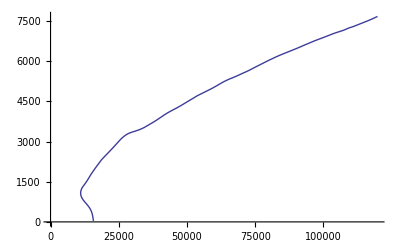
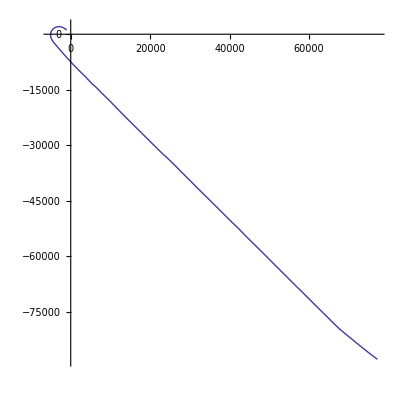

```mathematica
profile[2]
```

```mathematica
Take[trackmatrix[[1]],3]
```

{{TRACK 21895420},{11229198},{05/04/2011}}

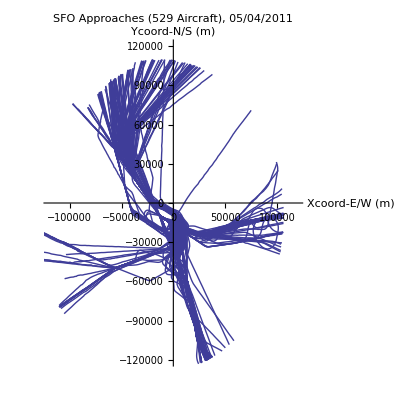

```mathematica
Show[Table[planar[indexlist[[i]]],{i,529}],PlotRange->{{-120000,120000},{-120000,120000}},PlotLabel->"SFO Approaches (529 Aircraft), 05/04/2011",AxesLabel->{ "Xcoord-E/W (m)","Ycoord-N/S (m)"}]
```

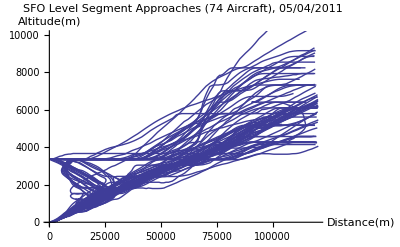

```mathematica
Show[Table[vert[indexlist[[flatties[[i]]]]],{i,1,74}],PlotRange->{{0,120000},{0,10000}},PlotLabel->"SFO Level Segment Approaches (74 Aircraft), 05/04/2011",AxesLabel->{ "Distance(m)","Altitude(m)"}]
```